```mathematica
(* 01 *)
```

594/7

```mathematica
(* 02 *)
N[%,2]
```

85.

```mathematica
NumberForm[84.85714285714286,2]
```

85.

```mathematica
(* 03 *)
steps1  = Table[i-1,{i,0,5}];
N[Median[steps1]]
```

1.5

```mathematica
(* 04 *)
Probability[
	x+y+z == 11,
	x\[Distributed]DiscreteUniformDistribution[{1,6}] &&
       y\[Distributed]DiscreteUniformDistribution[{1,6}] &&
       z\[Distributed]DiscreteUniformDistribution[{1,6}]  
]
```

1/8

```mathematica
Probability[
	x+y+z == 12,
	x\[Distributed]DiscreteUniformDistribution[{1,6}] &&
       y\[Distributed]DiscreteUniformDistribution[{1,6}] &&
       z\[Distributed]DiscreteUniformDistribution[{1,6}]  
]
```

25/216

```mathematica
(* 05 *)
BinomialDistribution[4,0.8]
```

BinomialDistribution[4,0.8]

```mathematica
CDF[BinomialDistribution[4,0.8],3]
```

0.5904

```mathematica
(* 06 *) (* -> 拉里伯德是谁？？ *)
(* 07 *)
labresults1 = Table[{2i-1,i^2-5i+1},{i,1,25,1}];
linearfit1 = Fit[labresults1,{1,x},x];
quadfit1 =Fit[labresults1,{1,x,x^2},x];
```

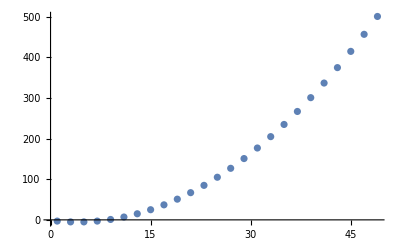

```mathematica
(* 08 *)
vislabresult = ListPlot[labresults1]
```

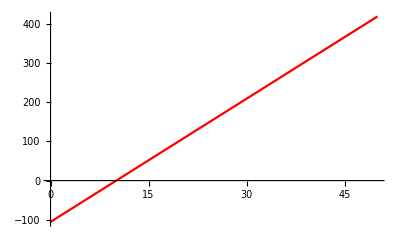

```mathematica
vislineearfit1 = Plot[linearfit1,{x,0,50},PlotStyle->Red]
```

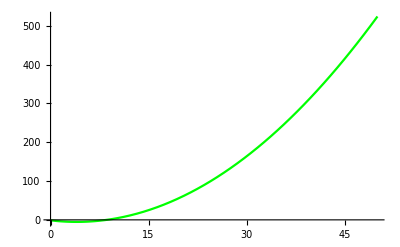

```mathematica
vislineearfit2 = Plot[quadfit1,{x,0,50},PlotStyle->Green]
```

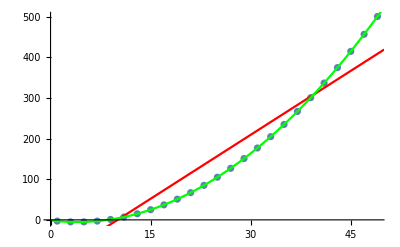

```mathematica
(* 09 *)
Show[vislabresult,vislineearfit1,vislineearfit2]
```

```mathematica
(* 10 *)
rolls = RandomChoice[{1,2,3,4,5,6},100]
```

{1,2,2,4,4,5,1,3,6,4,3,1,1,3,1,5,3,3,5,3,2,3,1,4,2,5,1,3,2,2,4,3,5,1,5,2,6,4,3,3,6,1,5,5,6,5,1,3,3,4,2,1,6,4,6,5,3,2,4,6,2,5,3,5,5,3,2,4,2,1,3,3,1,6,2,3,3,1,5,2,5,2,1,1,1,3,5,3,2,5,6,4,4,1,3,4,5,1,5,3}

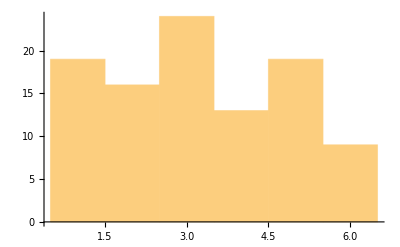

```mathematica
Histogram[rolls]
```